# A w Phantom Transition at z_t<0.1 as a Resolution to the Hubble Tension - G. Alestas, L. Kazantzidis and L. Perivolaropoulos - Figures 3-5

## Section III - Fitting LwPT to Cosmological Data and Comparison with wCDM

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,NMinimize::cvmit,NIntegrate::slwcon];
```

### Various Constants

```mathematica
(* TT,TE,EE+lowE Likelihoods - 4th column of arxiv:1807.06209 *)
H0pl=67.27;
h0pl=H0pl/100;
obh2pl=0.02236;
om0pl=0.3166;
or0pl=(1+3.046*7/8*(4/11)^(4/3)) 2.473*10^(-5);
σ8pl=0.812;
(* See arxiv:1903.07603 *)
H0riess=74.03;
h0riess=H0riess/100;
(* Other Constants *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
(* Dashing Options *)
d1=.025;
d2=.001;
```

## Data Points Lists

### BAO Data

```mathematica
datadv={{0.106,439.3,19.6},{0.44,1716,83},{0.60,2221,100},{0.73,2516,86},{0.15,664,25},{0.32,1270,14},{0.57,2033,21},{0.38,1477,16},{0.51,1877,19},{0.61,2140,22}};
```

## χ^2 Analysis for LwPT Dark Energy Model

```mathematica
(* Equivalent form of the LwPT Dark Energy Model as a function of α *)
w[a_,w0_,wa_,at_]:=w0+wa HeavisideTheta[1/a -1 /at]
(* Subscript[f, DE](α) for LwPT Dark Energy Model *)
f[a_,w0_,wa_,at_]:=ⅇ^(-3 ((1+w0) Log[a]+wa HeavisideTheta[1/a-1/at] Log[a/at]));
(* See Eq. (2) of arxiv:9709112 *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,at]]
(* Sound speed *) 
cs[a_?NumberQ,obh2_?NumberQ]:=c/√(3(1+(31500 obh2(Tcmb/2.7)^-4)a));
(* Redshift at decoupling - See Eqs. (66)-(68) of arxiv:0803.0547 *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift - see Eq. (4) of arxiv:9709112 *)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
(* Comoving sound horizon at drag redshift *)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2H[x,om,w0,wa,h,at]),{x,10^-11,1/(1+ze[om,obh2,h])}]
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(DLsol[om,w0,wa,h,at]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,h,at]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=(c/(100h)dL[z]/.DLsol[om,w0,wa,h,at])[[1]]//Chop
(* Angular diameter distance, see arxiv:0803.0547  *)
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=1/(1+z)^2 DL[z,om,w0,wa,h,at]
baoda[z_,om_,w0_,wa_,h_,at_?NumberQ]:= DA[z,om,w0,wa,h,at](rs[zdrag,om0pl,obh2pl,-1,0,h0pl,1]/rs[zdrag,om,obh2pl,w0,wa,h,at]);
(* Dilation scale *)
Dv[zbao_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=((DL[zbao,om,w0,wa,h,at]/(1+zbao))^2  (c*zbao)/H[1/(1+zbao),om,w0,wa,h,at])^(1/3)
(* BAO Subscript[d, z] ratio *)
dz[zbao_,om_,obh2_,w0_,wa_,h_,at_]:=rs[zdrag,om,obh2,w0,wa,h,at]/Dv[zbao,om,w0,wa,h,at]
(* DH "distance" *)
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=c/H[1/(1+z),om,w0,wa,h,at]
hz[z_,om_,w0_,wa_,h_,at_]:=H[1/(1+z),om,w0,wa,h,at]
baodv[z_,om_,w0_,wa_,h_,at_]:=rs[zdrag,om0pl,obh2pl,-1,0,h0pl,at]/dz[z,om,obh2pl,w0,wa,h,at];

(* Scaled distance at recombination *)
R[om_,obh2_,w0_,wa_,h_,at_]:=√(om (100h)^2)DA[zcmb[om,obh2,h],om,w0,wa,h,at](1+zcmb[om,obh2,h])/c
(* Angular scale of sound horizon at recombination *)
la[om_,obh2_,w0_,wa_,h_,at_]:=π (DA[zcmb[om,obh2,h],om,w0,wa,h,at](1+zcmb[om,obh2,h]))/(rs[zcmb,om,obh2,w0,wa,h,at])
```

### Individual χ^2

#### CMB χ^2

```mathematica
(* Central values for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck18/ΛCDM - See Eq. (31) on page 7 of arxiv:1811.07425 *)
datacmb={1.74963,301.80845,0.02237};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{1598.9554, 17112.007, −36.311179}, {17112.007, 811208.45, −494.79813}, {-36.311179, -494.79813, 2.1242182}});
invcovcmb=Inverse[covcmb];
(* χ^2 for CMB *)
vec[om_,obh2_,w0_,wa_,h_,at_]:={R[om,obh2,w0,wa,h,at]-datacmb[[1]],la[om,obh2,w0,wa,h,at]-datacmb[[2]],obh2-datacmb[[3]]};
chi2R[om_,obh2_,w0_,wa_,h_,at_]:=vec[om,obh2,w0,wa,h,at].invcovcmb.vec[om,obh2,w0,wa,h,at]
```

#### Cosmic Chronometers χ^2

```mathematica
(* Cosmic Chronometers data from arxiv:1709.00646 *)
dataHz=Join[Import[".\\data\\Hz_all_Moresco.dat","Table"],Import[".\\data\\Hz_clustering.txt","Table"],Import[".\\data\\1610.01202.txt","Table"]];
(* χ^2 for Cosmic Chronometers *)
chi2cc[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=Sum[(1/dataHz[[i,3]](dataHz[[i,2]]-hz[dataHz[[i,1]],om,w0,wa,h,at]))^2,{i,1,Length[dataHz]}];
```

#### BAO χ^2

```mathematica
(* 6dFGs and WiggleZ BAO data - See arxiv:1605.02702 on page 6 *)
databao={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv=({{1/databao[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
vecbao[om_,obh2_,w0_,wa__,h_,at_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,obh2,w0,wa,h,at]),{i,1,Length[databao]}];
```

```mathematica
(*(Dv/rs)- arxiv:1409.3242 and (Dv/rs)- arxiv:1312.4877 *)
dataSDSS={{0.15,4.465666824,0.1681350461},{0.32,8.62,0.15},{0.57,13.70,0.12}};
(* BAO measurements from Lya are {Da/rs, DH/rs} - arxiv:1904.03400 *)
dataLya={{2.34,11.28,0.65},{2.34,9.18,0.28}};
CijLyainv=({{1/dataLya[[1,3]]^2, 0}, {0, 1/dataLya[[2,3]]^2}});
vecLya[om_,obh2_,w0_,wa_,h_,at_]:={dataLya[[1,2]]-DA[dataLya[[1,1]],om,w0,wa,h,at]/rs[zdrag,om,obh2,w0,wa,h,at],dataLya[[2,2]]-DH[dataLya[[2,1]],om,w0,wa,h,at]/rs[zdrag,om,obh2,w0,wa,h,at]};
(* Total length of BAO datapoints *)
ndatBAO=Length[dataSDSS]+Length[databao]+Length[dataLya];
```

```mathematica
(* Total BAO χ^2 *)
chi2bao[om_,obh2_,w0_,wa_,h_,at_]:=vecbao[om,obh2,w0,wa,h,at].Cijbaoinv.vecbao[om,obh2,w0,wa,h,at]+Sum[(dataSDSS[[i,2]]-1/dz[dataSDSS[[i,1]],om,obh2,w0,wa,h,at])^2/dataSDSS[[i,3]]^2,{i,1,Length[dataSDSS]}]+vecLya[om,obh2,w0,wa,h,at].CijLyainv.vecLya[om,obh2,w0,wa,h,at]
```

#### Full Pantheon χ^2

```mathematica
(* Import the Full Pantheon Data *)
dataPanth=Import[".\\data\\lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
Dij0=Import[".\\data\\sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Id=ConstantArray[1,ndatPanth];
(* Statistical Uncertainties *)
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
(* Systematic Uncertainties *)
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

```mathematica
(* χ^2 Formula for Full Pantheon Data *)
chi2Panth[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,at_?NumberQ]:=
Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(M+5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],om,w0,wa,h0riess,at]]+25),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.
(* χ^2 for ΛCDM Model using the full Pantheon data *)
minPanthlcdm=NMinimize[{chi2Panth[M,om,-1,0,1],-19.5<M<-19. && 0.25<om<0.35},{M,om}]//AbsoluteTiming;
MPanthlcdm=minPanthlcdm[[2,2,1,2]];
*)
```

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
minPanthlcdm={127.5417684,{1025.6256891803512,{M->-19.228493256576748,om->0.29890280558640075}}};
MPanthlcdm=minPanthlcdm[[2,2,1,2]];
omPanthlcdm=minPanthlcdm[[2,2,2,2]];
```

### Total χ^2 for LwPT DE Model for various z_t

```mathematica
(* Construct the total χ^2 as a sum of the individual χ^2 *)
chi2total[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=chi2R[om,obh2pl,w0,wa,h,at]+chi2bao[om,obh2pl,w0,wa,h,at]+chi2cc[om,w0,wa,h,at]+ chi2Panth[M,om,w0,wa,at]
ndatCMB=Length[datacmb];ndatcc=Length[dataHz];
(* Total number of data *)
ndatot=ndatCMB+ndatBAO+ndatPanth+ndatcc
```

1101

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.
(* χ^2 for uΛCDM Model using all the data *)
minlcdm=NMinimize[{chi2total[MPanthlcdm,om,-1,0,h,1],0.25<om<0.35 && 0.65<h<0.75},{om,h}]//AbsoluteTiming;
ombf=minlcdm[[2,2,1,2]];
hbf=minlcdm[[2,2,2,2]];
chifun=ListInterpolation[ParallelTable[chi2total[MPanthlcdm,om,-1,0,h,1],{om,ombf-0.02,ombf+0.02,0.02},{h,hbf-0.02,hbf+0.02,0.02},DistributedContexts->Automatic],{{ombf-0.02,ombf+0.02},{hbf-0.02,hbf+0.02}}];
(* Params that we want to calculate the errors *)
params={om,h};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[om,h],params[[p]],params[[d]]]/.minlcdm[[2,2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
Print["The best fit parameters for Ω_(0 m) and h are: Ω_(0 m)=",ombf,"±",errors[[1]]," and h=",hbf,"±",errors[[2]]," respectively"]
*)
```

The best fit parameters for Ω_(0  m) and h are: Ω_(0  m)=0.311721±0.00586442 and h=0.675791±0.00396596 respectively

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
minlcdm={1238.4919571,{1070.4208728386325,{om->0.3117207297272851,h->0.6757906631845788}}};
ombflcdm=minlcdm[[2,2,1,2]];
hbflcdm=minlcdm[[2,2,2,2]];
```

### χ^2 Calculations for LwPT DE Model for various z_t

```mathematica
(* Select the corresponding Subscript[z, t] values for Subscript[z, t]<0.15 *)
ztlist1=Table[i,{i,0.001,0.15,0.005}];
(* Select the corresponding Subscript[z, t] values for 0.15<Subscript[z, t]<1.7 *)
ztlist2=Table[i,{i,0.15,1.7,0.1}];
(* Join the two lists *)
ztlist=Join[ztlist1,ztlist2]
Length[ztlist]
```

{0.001,0.006,0.011,0.016,0.021,0.026,0.031,0.036,0.041,0.046,0.051,0.056,0.061,0.066,0.071,0.076,0.081,0.086,0.091,0.096,0.101,0.106,0.111,0.116,0.121,0.126,0.131,0.136,0.141,0.146,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65}

46

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.
(* Do loop to obtain the best fit values of (M, Subscript[Ω, 0m], Subscript[w, 0], Subscript[w, a]) for h=Subscript[h, 0,riess] through NMinimize. This cell takes some time to be completed. Therefore, you can use the following table to run the program without going through the (time-consuming) data acquisition process *)
(*mintot={};ztdchiw0walist={};
Do[minhsd=NMinimize[{chi2total[M,om,w0,wa,h0riess,1/(1+ztlist[[p]])],-19.6<M<-19,0.25<om<0.35},{M,om,w0,wa}];
dchi=minhsd[[1]]-minlcdm[[2,1]];
om0=minhsd[[2,2,2]];
w00=minhsd[[2,3,2]];
waa=minhsd[[2,4,2]];
omh2=minhsd[[2,2,2]]*h0riess^2;
AppendTo[mintot,minhsd];
AppendTo[ztdchiw0walist,{ztlist[[p]],dchi,w00,waa,w00+waa,om0,omh2}];
If[Mod[p,9]==0,Print["Finished step ",p," of ",Length[ztlist], " realizations // Δχ^2=",dchi,", w_0+w_a=",w00+waa," and Ω_(0 m)h^2=",omh2" for z_t=",ztlist[[p]]]],{p,1,Length[ztlist]}]*)
*)
```

Finished step 9 of 46 realizations // Δχ^2=23.5659, w_0+w_a=-1.03862 and Ω_(0  m)h^2=0.142852  for z_t=0.041

Finished step 18 of 46 realizations // Δχ^2=39.7133, w_0+w_a=-1.09409 and Ω_(0  m)h^2=0.142993  for z_t=0.086

Finished step 27 of 46 realizations // Δχ^2=48.1617, w_0+w_a=-1.16405 and Ω_(0  m)h^2=0.143321  for z_t=0.131

Finished step 36 of 46 realizations // Δχ^2=49.6041, w_0+w_a=-1.33192 and Ω_(0  m)h^2=0.143957  for z_t=0.65

Finished step 45 of 46 realizations // Δχ^2=45.1572, w_0+w_a=-5.282 and Ω_(0  m)h^2=0.144198  for z_t=1.55

```mathematica
(* The results of the Do loop
(*ztdchiw0walist
{{0.001,-2.6237510259531973,-84.69618606337538,83.68269495195692,-1.0134911114184604,0.26111759332968515,0.1431039538193574},{0.006,-1.5877721787044266,-15.65640872795191,14.652809961329222,-1.0035987666226873,0.26094497204834377,0.14300934974631002},{0.011,1.643620789076067,-9.107655537615669,8.106564957599426,-1.0010905800162426,0.26082466471128185,0.1429434160212496},{0.016,6.2813181624248955,-6.456030730619987,5.449588310775058,-1.0064424198449293,0.2607645184098277,0.14291045319620227},{0.021,10.498426444157985,-5.05142806385136,4.038651645740794,-1.0127764181105663,0.26071925066272605,0.14288564447493562},{0.026000000000000002,14.25302411902635,-4.193626224646599,3.1747621825016874,-1.0188640421449118,0.2606829456299845,0.14286574771630436},{0.031,17.769119110906104,-3.6049076782881513,2.579132943229238,-1.0257747350589135,0.2606648711926704,0.1428558421277543},{0.036000000000000004,20.87674620479811,-3.1852948554757847,2.152908833891834,-1.0323860215839509,0.26065668235557915,0.14285135428398246},{0.041,23.56593032768228,-2.8735146817845787,1.8348934872245506,-1.038621194560028,0.26065717448281017,0.14285162399140294},{0.046,25.874245481924163,-2.6353597116148904,1.59103546291357,-1.0443242487013205,0.26066233007874434,0.14285444948528508},{0.051000000000000004,27.964842193676304,-2.446558943762028,1.396733986268571,-1.049824957493457,0.26067293494042654,0.1428602614170553},{0.056,29.874682783103708,-2.293463635781619,1.2382933700348782,-1.0551702657467408,0.2606879771545824,0.14286850521362393},{0.061,31.690771189106954,-2.1642500861711413,1.1033910315695965,-1.0608590546015448,0.260710315085692,0.14288074738475134},{0.066,33.442313772164425,-2.0506662819355386,0.9832480152167034,-1.0674182667188352,0.2607430827042769,0.14289870548446018},{0.07100000000000001,35.121860019988844,-1.9578974404815608,0.8847175277013654,-1.0731799127801955,0.2607744462660895,0.14291589409915292},{0.076,36.72161783303932,-1.874189185966481,0.7944290026808937,-1.0797601832855874,0.2608149998757172,0.14293811926523758},{0.081,38.25868061913684,-1.8001994327838509,0.7135548184570817,-1.0866446143267692,0.2608612103794593,0.14296344465870936},{0.08600000000000001,39.713341985139095,-1.7332131396269181,0.6391204576553752,-1.094092681971543,0.26091437202114975,0.1429925795822525},{0.091,41.07310711325658,-1.6738293386719625,0.5721730599352081,-1.1016562787367543,0.26097115612026195,0.1430236997721769},{0.096,42.340933800012635,-1.6204458928094168,0.5109932364304965,-1.1094526563789202,0.2610324102286143,0.14305726972424762},{0.101,43.49917055785181,-1.572493702792971,0.455100809313336,-1.117392893479635,0.2610969964962374,0.14309266584651364},{0.106,44.541729759011105,-1.5295785739511742,0.4042269976908741,-1.1253515762603001,0.26116370288359847,0.14312922388787214},{0.111,45.48478698745748,-1.4909507264458275,0.3575861390092384,-1.133364587436589,0.2612337198598684,0.1431675962779165},{0.116,46.307583209147424,-1.4564919649955732,0.31523724406820564,-1.1412547209273676,0.2613038661434762,0.14320603953408326},{0.121,47.0210615249357,-1.4257317402009189,0.276736597111895,-1.148995143089024,0.26137393852215,0.1432444422870877},{0.126,47.63621882403754,-1.3982222289814055,0.24163980524198178,-1.1565824237394238,0.2614438249280276,0.1432827431188002},{0.131,48.16167016490226,-1.373477467775684,0.2094232243547966,-1.1640542434208874,0.26151354656914055,0.14332095365215727},{0.136,48.604332127098814,-1.3513733044368934,0.18005132489612471,-1.1713219795407688,0.2615823983073864,0.14335868744038913},{0.14100000000000001,48.96959894047109,-1.3317176228604166,0.1533858727870594,-1.1783317500733572,0.2616494095217145,0.1433954125403654},{0.146,49.261430690409725,-1.313962492048921,0.12875708732515745,-1.1852054047237637,0.261714950171034,0.1434313317058797},{0.15,49.44947956099054,-1.3027099877100987,0.11297576391252577,-1.189734223797573,0.26176056066433157,0.14345632826717342},{0.25,49.874711637060045,-1.202649386516834,-0.05690194026877829,-1.2595513267856122,0.26245738587095974,0.143838219203429},{0.35,49.82932236891838,-1.2068783244141612,-0.0643626483405836,-1.271240972754745,0.26252148121130714,0.14387334627590295},{0.45000000000000007,49.739758947671135,-1.2083382685011332,-0.08032175826879046,-1.2886600267699237,0.2625999713425907,0.14391636232847624},{0.55,49.790280359246935,-1.2133789700332198,-0.08096417744204153,-1.2943431474752614,0.26257939098450817,0.143905083384859},{0.65,49.604059430114376,-1.2108278393318357,-0.12109038289448408,-1.3319182222263197,0.26267495626452503,0.14395745737178145},{0.7500000000000001,49.29946229815437,-1.2068755004312817,-0.18880728068357336,-1.395682781114855,0.26279366845621205,0.14402251688684647},{0.8500000000000001,48.87200203134603,-1.2025210877657648,-0.2924671646998329,-1.4949882524655977,0.26292487465893916,0.1440944236708224},{0.9500000000000001,48.37989147166422,-1.19874140784272,-0.4384060732339081,-1.6371474810766282,0.2630402912311542,0.1441576770411129},{1.05,47.769842331049176,-1.1950911708963985,-0.6604569778964436,-1.8555481487928422,0.2631539734253585,0.1442199798957848},{1.15,47.18243448177304,-1.1929455220879992,-0.9623316829206543,-2.1552772050086535,0.2632204765013788,0.14425642651356455},{1.25,46.445144073689335,-1.1909493042824626,-1.4595774517929907,-2.650526756075453,0.2632789039488546,0.14428844733084745},{1.35,45.667361245734355,-1.189764276745097,-2.302566069581704,-3.492330346326801,0.26330732817794383,0.1443040250616126},{1.45,45.138924907611454,-1.1904791532544519,-3.6033284239616585,-4.793807577216111,0.2632728823105427,0.1442851472075585},{1.55,45.157177527041995,-1.195406826779915,-4.086590605617516,-5.281997432397431,0.2631138918783335,0.1441980134408197},{1.65,44.83000566001647,-1.1981540573108136,-5.646721564350561,-6.844875621661375,0.26301567527774605,0.14414418641332785}}*)
*)
```

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
ztdchiw0walist={{0.001,-2.6237510259531973,-84.69618606337538,83.68269495195692,-1.0134911114184604,0.26111759332968515,0.1431039538193574},{0.006,-1.5877721787044266,-15.65640872795191,14.652809961329222,-1.0035987666226873,0.26094497204834377,0.14300934974631002},{0.011,1.643620789076067,-9.107655537615669,8.106564957599426,-1.0010905800162426,0.26082466471128185,0.1429434160212496},{0.016,6.2813181624248955,-6.456030730619987,5.449588310775058,-1.0064424198449293,0.2607645184098277,0.14291045319620227},{0.021,10.498426444157985,-5.05142806385136,4.038651645740794,-1.0127764181105663,0.26071925066272605,0.14288564447493562},{0.026000000000000002,14.25302411902635,-4.193626224646599,3.1747621825016874,-1.0188640421449118,0.2606829456299845,0.14286574771630436},{0.031,17.769119110906104,-3.6049076782881513,2.579132943229238,-1.0257747350589135,0.2606648711926704,0.1428558421277543},{0.036000000000000004,20.87674620479811,-3.1852948554757847,2.152908833891834,-1.0323860215839509,0.26065668235557915,0.14285135428398246},{0.041,23.56593032768228,-2.8735146817845787,1.8348934872245506,-1.038621194560028,0.26065717448281017,0.14285162399140294},{0.046,25.874245481924163,-2.6353597116148904,1.59103546291357,-1.0443242487013205,0.26066233007874434,0.14285444948528508},{0.051000000000000004,27.964842193676304,-2.446558943762028,1.396733986268571,-1.049824957493457,0.26067293494042654,0.1428602614170553},{0.056,29.874682783103708,-2.293463635781619,1.2382933700348782,-1.0551702657467408,0.2606879771545824,0.14286850521362393},{0.061,31.690771189106954,-2.1642500861711413,1.1033910315695965,-1.0608590546015448,0.260710315085692,0.14288074738475134},{0.066,33.442313772164425,-2.0506662819355386,0.9832480152167034,-1.0674182667188352,0.2607430827042769,0.14289870548446018},{0.07100000000000001,35.121860019988844,-1.9578974404815608,0.8847175277013654,-1.0731799127801955,0.2607744462660895,0.14291589409915292},{0.076,36.72161783303932,-1.874189185966481,0.7944290026808937,-1.0797601832855874,0.2608149998757172,0.14293811926523758},{0.081,38.25868061913684,-1.8001994327838509,0.7135548184570817,-1.0866446143267692,0.2608612103794593,0.14296344465870936},{0.08600000000000001,39.713341985139095,-1.7332131396269181,0.6391204576553752,-1.094092681971543,0.26091437202114975,0.1429925795822525},{0.091,41.07310711325658,-1.6738293386719625,0.5721730599352081,-1.1016562787367543,0.26097115612026195,0.1430236997721769},{0.096,42.340933800012635,-1.6204458928094168,0.5109932364304965,-1.1094526563789202,0.2610324102286143,0.14305726972424762},{0.101,43.49917055785181,-1.572493702792971,0.455100809313336,-1.117392893479635,0.2610969964962374,0.14309266584651364},{0.106,44.541729759011105,-1.5295785739511742,0.4042269976908741,-1.1253515762603001,0.26116370288359847,0.14312922388787214},{0.111,45.48478698745748,-1.4909507264458275,0.3575861390092384,-1.133364587436589,0.2612337198598684,0.1431675962779165},{0.116,46.307583209147424,-1.4564919649955732,0.31523724406820564,-1.1412547209273676,0.2613038661434762,0.14320603953408326},{0.121,47.0210615249357,-1.4257317402009189,0.276736597111895,-1.148995143089024,0.26137393852215,0.1432444422870877},{0.126,47.63621882403754,-1.3982222289814055,0.24163980524198178,-1.1565824237394238,0.2614438249280276,0.1432827431188002},{0.131,48.16167016490226,-1.373477467775684,0.2094232243547966,-1.1640542434208874,0.26151354656914055,0.14332095365215727},{0.136,48.604332127098814,-1.3513733044368934,0.18005132489612471,-1.1713219795407688,0.2615823983073864,0.14335868744038913},{0.14100000000000001,48.96959894047109,-1.3317176228604166,0.1533858727870594,-1.1783317500733572,0.2616494095217145,0.1433954125403654},{0.146,49.261430690409725,-1.313962492048921,0.12875708732515745,-1.1852054047237637,0.261714950171034,0.1434313317058797},{0.15,49.44947956099054,-1.3027099877100987,0.11297576391252577,-1.189734223797573,0.26176056066433157,0.14345632826717342},{0.25,49.874711637060045,-1.202649386516834,-0.05690194026877829,-1.2595513267856122,0.26245738587095974,0.143838219203429},{0.35,49.82932236891838,-1.2068783244141612,-0.0643626483405836,-1.271240972754745,0.26252148121130714,0.14387334627590295},{0.45000000000000007,49.739758947671135,-1.2083382685011332,-0.08032175826879046,-1.2886600267699237,0.2625999713425907,0.14391636232847624},{0.55,49.790280359246935,-1.2133789700332198,-0.08096417744204153,-1.2943431474752614,0.26257939098450817,0.143905083384859},{0.65,49.604059430114376,-1.2108278393318357,-0.12109038289448408,-1.3319182222263197,0.26267495626452503,0.14395745737178145},{0.7500000000000001,49.29946229815437,-1.2068755004312817,-0.18880728068357336,-1.395682781114855,0.26279366845621205,0.14402251688684647},{0.8500000000000001,48.87200203134603,-1.2025210877657648,-0.2924671646998329,-1.4949882524655977,0.26292487465893916,0.1440944236708224},{0.9500000000000001,48.37989147166422,-1.19874140784272,-0.4384060732339081,-1.6371474810766282,0.2630402912311542,0.1441576770411129},{1.05,47.769842331049176,-1.1950911708963985,-0.6604569778964436,-1.8555481487928422,0.2631539734253585,0.1442199798957848},{1.15,47.18243448177304,-1.1929455220879992,-0.9623316829206543,-2.1552772050086535,0.2632204765013788,0.14425642651356455},{1.25,46.445144073689335,-1.1909493042824626,-1.4595774517929907,-2.650526756075453,0.2632789039488546,0.14428844733084745},{1.35,45.667361245734355,-1.189764276745097,-2.302566069581704,-3.492330346326801,0.26330732817794383,0.1443040250616126},{1.45,45.138924907611454,-1.1904791532544519,-3.6033284239616585,-4.793807577216111,0.2632728823105427,0.1442851472075585},{1.55,45.157177527041995,-1.195406826779915,-4.086590605617516,-5.281997432397431,0.2631138918783335,0.1441980134408197},{1.65,44.83000566001647,-1.1981540573108136,-5.646721564350561,-6.844875621661375,0.26301567527774605,0.14414418641332785}};
```

### χ^2 Calculations for LwPT DE Model for various z_t

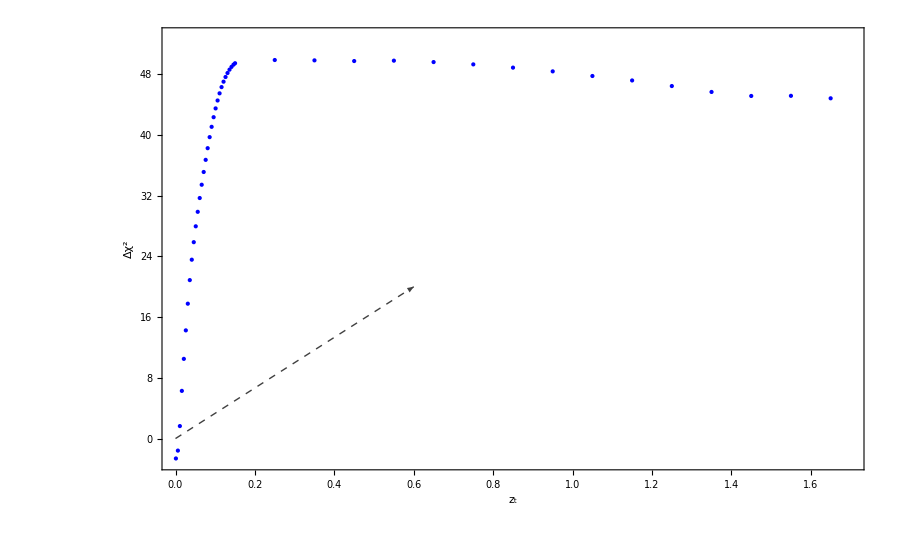

```mathematica
(* Δχ^2=f(Subscript[z, t]) plot *)
ztdchilist=Table[{ztdchiw0walist[[p,1]],ztdchiw0walist[[p,2]]},{p,1,Length[ztdchiw0walist]}];
ztdchiplt=ListPlot[ztdchilist, Frame->True,FrameLabel->{"z_t","Δχ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->Large,Blue},ImageSize->900,PlotRange->{{0,1.7},{-3,53}}, FrameStyle -> Directive[Black, Thick]];
ztdchipltsmall=ListPlot[ztdchilist, Frame->True,FrameLabel->{"z_t","Δχ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->Large,Blue},ImageSize->500, PlotRange->{{0,0.015},{-3,3}}, FrameStyle -> Directive[Black, Thick],FrameTicks->{{{-3,-2,-1, 0, 1, 2 ,3},None},{{0,0.006,0.012},None}}];
ztdchi=Show[ztdchiplt,Epilog->{Inset[ztdchipltsmall,Scaled[{0.65,0.53}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{0,0},{0.6,20}}]},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large]]
```

## wCDM Model for w=-1.22 and h=h_(0,riess)

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.
minwcdmfxd=NMinimize[{chi2total[M,om,-1.22,0,h0riess,1],-19.6<M<-19,0.25<om<0.35},{M,om}] //AbsoluteTiming
dchiwcdmfxd=minwcdmfxd[[2,1]]-minlcdm[[2,1]]
*)
```

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
minwcdmfxd={606.0565754,{1120.9756388630938,{M->-19.295180033547027,om->0.26113209171258495}}};
Mwcdmfxd=minwcdmfxd[[2,2,1,2]];
omwcdmfxd=minwcdmfxd[[2,2,2,2]];
dchiwcdmfxd=50.55476602446129;
```

### Figure 3

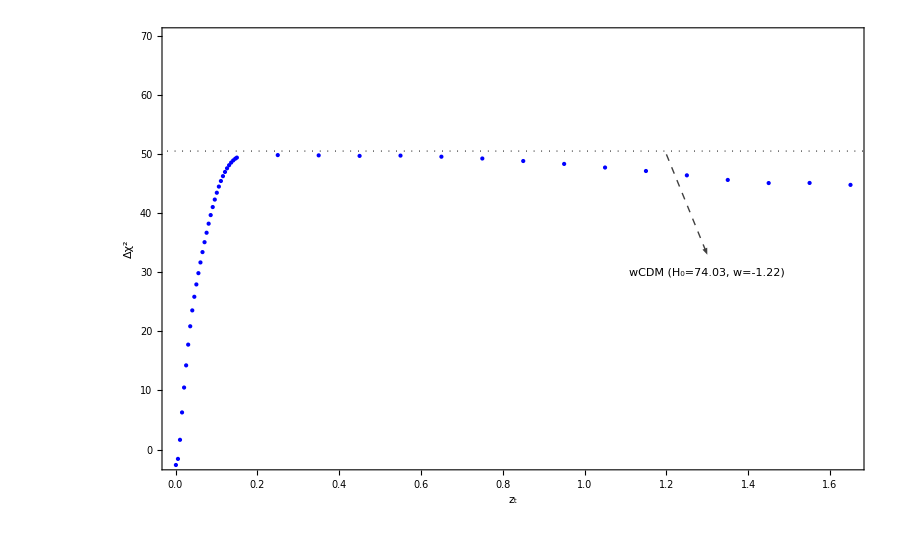

```mathematica
dchi2=Show[ztdchiplt,PlotRange->{{0,1.65},{-2,70}},Prolog->{{Black,Thick,Dotted,Line[{{-5,dchiwcdmfxd},{2,dchiwcdmfxd}}]}},Epilog->{Text["wCDM (H_0=74.03, w=-1.22)",{1.3,30}],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{1.2,50},{1.3,33}}]},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large]]
```

```mathematica
Export[NotebookDirectory[]<>"dchi2plot.pdf",dchi2,ImageResolution->1000];
```

## Comoving Hubble Parameter for various DE models

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.
(*minhsd005=NMinimize[{chi2total[M,om,w0,wa,h0riess,1/(1+0.005)],-19.6<M<-19,0.25<om<0.35},{M,om,w0,wa}] //AbsoluteTiming
Mbfhsd=minhsd005[[2,2,1,2]];
ombfhsd=minhsd005[[2,2,2,2]];
w0bfhsd=minhsd005[[2,2,3,2]];
wabfhsd=minhsd005[[2,2,4,2]];
chifunhsd=ListInterpolation[ParallelTable[chi2total[M,om,w0,wa,h0riess,1/(1+0.005)],{M,Mbfhsd-0.06,Mbfhsd+0.06,0.02},{om,ombfhsd-0.06,ombfhsd+0.06,0.02},{w0,w0bfhsd-0.06,w0bfhsd+0.06,0.02},{wa,wabfhsd-0.06,wabfhsd+0.06,0.02},DistributedContexts->Automatic],{{Mbfhsd-0.06,Mbfhsd+0.06},{ombfhsd-0.06,ombfhsd+0.06},{w0bfhsd-0.06,w0bfhsd+0.06},{wabfhsd-0.06,wabfhsd+0.06}}];
(* Params that we want to calculate the errors *)
paramshsd={M,om,w0,wa};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijhsd=1/2 Table[D[chifunhsd[M,om,w0,wa],paramshsd[[p]],paramshsd[[d]]]/.minhsd005[[2,2]],{p,1,Length[paramshsd]},{d,1,Length[paramshsd]}];
cijhsd=Inverse[Fijhsd];
errorshsd=Sqrt[Diagonal[cijhsd]];
Print["The best fit parameters for M, Ω_(0 m), w_0 and w_a are: M=",Mbfhsd,"±",errorshsd[[1]],", Ω_(0 m)=",ombfhsd,"±",errorshsd[[2]],", w_0=",w0bfhsd,"±",errorshsd[[3]]," and w_a=",wabfhsd,"±",errorshsd[[4]]," respectively."]*)
*)
```

The best fit parameters for M, Ω_(0  m), w_0 and w_a are: M=-19.4197±0.00440984, Ω_(0  m)=0.260977±0.0014925, w_0=-18.4426±0.100136 and w_a=17.4373±0.101344 respectively.

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
minhsd005={1756.3663217,{1068.464813885666,{M->-19.419655001950062,om->0.26097743240477395,w0->-18.442567843142214,wa->17.437291137251044}}};
Mbfhsd005=minhsd005[[2,2,1,2]];
ombfhsd005=minhsd005[[2,2,2,2]];
w0bfhsd005=minhsd005[[2,2,3,2]];
wabfhsd005=minhsd005[[2,2,4,2]];
```

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
minhsd05={1097.9825170875865,{M->-19.367347575067818,om->0.2606705104030203,w0->-2.481016897643636,wa->1.4322661859971197}};
minhsd05[[1]]-minlcdm[[2,1]]
Mbfhsd05=minhsd05[[2,1,2]];
ombfhsd05=minhsd05[[2,2,2]];
w0bfhsd05=minhsd05[[2,3,2]];
wabfhsd05=minhsd05[[2,4,2]];
```

27.5616

### Figure 4

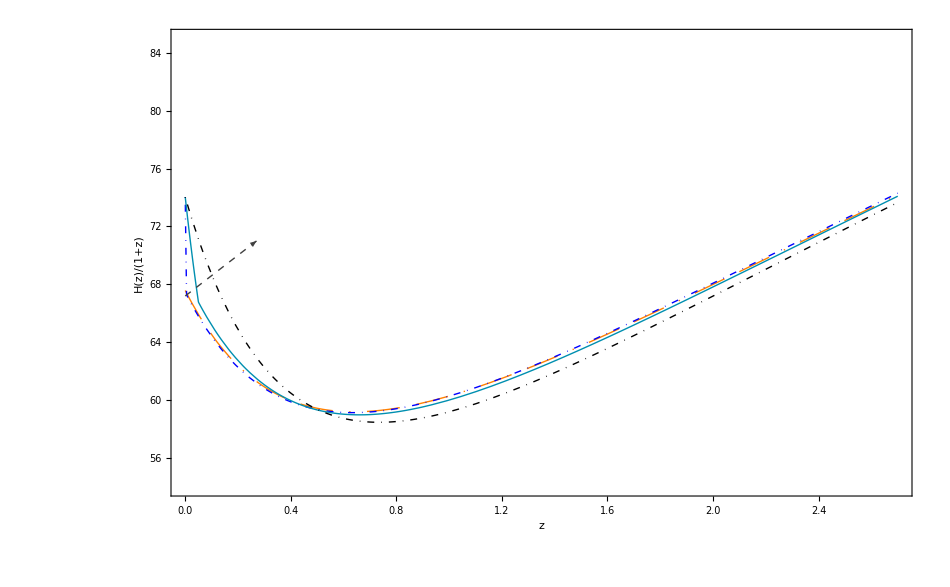

```mathematica
plHz1=Show[comHulcdm,comHhsd005,comHhsd05,comHwcdm,Graphics[{Dashed,Line[{{0,100*minlcdm[[2,2,2,2]]},{2.7,100*minlcdm[[2,2,2,2]]}}]}],PlotRange->{{0,0.5},{55,75}},Ticks->{Automatic,Range[54,78,2]},Frame->True,FrameLabel->{"z","H(z)/(1+z)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Axes->False,ImageSize->480];
plHz=Show[comHulcdm,comHhsd005,comHhsd05,comHwcdm,PlotRange->{54,85},Frame->True,FrameLabel->{"z","H(z)/(1+z)"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->950,Axes->False,Prolog->Inset[Framed[Column[{LineLegend[{{Directive[Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Orange]},Thick},{"uΛCDM Model"}]LineLegend[{Directive[DotDashed,Blue],Thick},{"LwPT Model (z_t=0.005)"}],LineLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],RGBColor[0.,0.56,0.69]],Thick},{"LwPT Model (z_t=0.05)"}]LineLegend[{Directive[DotDashed,Black],Thick},{"wCDM Model"}]}],RoundingRadius->5],Scaled[{0.77,0.14}],BaseStyle -> {FontFamily->"Times",10}],Epilog->{Inset[plHz1,Scaled[{0.37,0.675}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{0.,67.2},{0.27,71}}]}]
```

```mathematica
Export["comHzplt.pdf",plHz,ImageResolution->1000,ImageSize->850];
```

## Individual BAO and Pantheon Plot

### ΔD_V(z)(r_s^fid/r_s)Plot

```mathematica
zt02={0.02,-5.275206744040993,4.263663025664592,-1.0115437183764007,0.26072777948942966,0.14289031864800517,-19.402241567916423,9.697755107531293};
Mbfhsd02=zt02[[7]];
ombfhsd02=zt02[[5]];
w0bfhsd02=zt02[[2]];
wabfhsd02=zt02[[3]];
```

```mathematica
(* uΛCDM Plot *)
pldvulcdm=Plot[baodv[z,ombflcdm,-1,0,hbflcdm,1]-baodv[z,ombflcdm,-1,0,hbflcdm,1],{z,0.01,3.5},Frame->True,FrameLabel->{"z","ΔD(z)(r_s^fid/r_s) [Mpc]"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Orange,Thick},ImageSize->500,Axes->False];
(* LwPT DE Plot with Subscript[z, t]=0.005 *)
pldvhsd005=Plot[baodv[z,ombfhsd005,w0bfhsd005,wabfhsd005,h0riess,1/(1+0.005)]-baodv[z,ombflcdm,-1,0,hbflcdm,1],{z,0.01,3.5},Frame->True,FrameLabel->{"z","ΔD(z)(r_s^fid/r_s) [Mpc]"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{DotDashed,Blue,Thick},ImageSize->500,Axes->False];
(* LwPT DE Plot with Subscript[z, t]=0.02 *)
pldvhsd02=Plot[baodv[z,ombfhsd02,w0bfhsd02,wabfhsd02,h0riess,1/(1+0.02)]-baodv[z,ombflcdm,-1,0,hbflcdm,1],{z,0.01,3.5},Frame->True,FrameLabel->{"z","ΔD(z)(r_s^fid/r_s) [Mpc]"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Dashed,RGBColor[0,0.5,0],Thick},ImageSize->500,Axes->False];
(* wCDM DE plot with w=-1.22 *)
pldvwcdm=Plot[baodv[z,omwcdmfxd,-1.22,0,h0riess,1]-baodv[z,ombflcdm,-1,0,hbflcdm,1],{z,0.01,3.5},Frame->True,FrameLabel->{"z","ΔD(z)(r_s^fid/r_s) [Mpc]"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Black,Dotted,Thick},ImageSize->500,Axes->False];
```

```mathematica
(* ListPlot of BAO Data *)
dvdat=Table[{datadv[[i,1]],Around[datadv[[i,2]]-baodv[datadv[[i,1]],om0pl,-1,0,h0pl,1],datadv[[i,3]]]},{i,1,Length[datadv]}];
pldvdat=ListPlot[dvdat,Frame->True,FrameLabel->{"z","ΔD(z)(r_s^fid/r_s) [Mpc]"},BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Purple},ImageSize->Large];
```

```mathematica
(* Subscript[ΔD, V](z)(Subscript[r, s]^fid/Subscript[r, s]) Plot *)
dvBAOall=Show[pldvhsd005,pldvhsd02,pldvulcdm,pldvwcdm,pldvdat,ImageSize->480,PlotRange->{-60,20},FrameLabel->{"",""},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Epilog->{Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{0.8,0},{1.3,-35}}],Text["uΛCDM (Ω_(0  m)=0.312±0.006, 
             H_0=67.579±0.397)",{1.85,-43.2}],Arrow[{{0.76,6.2},{1.75,-8}}],Text["LwPT Model (Ω_(0  m)=0.261±0.001,
H_0=74.03, z_t=0.005)",{2.4,-18}]}];
```

```mathematica
dvplot=Show[pldvhsd005,pldvhsd02,pldvulcdm,pldvwcdm,pldvdat,ImageSize->1000,PlotRange->{-180,300},Epilog->{Inset[dvBAOall,Scaled[{0.7,0.675}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{0.1,0},{1.5,160}}],Arrow[{{0.8,-18},{1,-140}}],Arrow[{{0.1,-5},{1.3,-80}}]},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],Prolog->{Text["wCDM Model (H_0=74.03, w=-1.22)",{1.5,-150}],Text["LwPT Model (Ω_(0  m)=0.261±0.001, H_0=74.03, z_t=0.02)",{2.15,-88}]}];
```

### Δm(z)Plot

```mathematica
errall=Sqrt[Diagonal[Cijtot]];
panthdat=Table[{dataPanth[[1+i,2]],Around[dataPanth[[1+i,5]]-(MPanthlcdm+5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DL[dataPanth[[1+i,2]],omPanthlcdm,-1,0,h0riess,1]]+25),errall[[i]]]},{i,1,ndatPanth}];
(* ListPlot of Full Pantheon Data *)
mbplt=ListPlot[panthdat,Frame->True,FrameLabel->{"z","TraditionalForm`Δm(z)"},BaseStyle->FontSize->16,PlotRange->{{0,2.3},{-1,1}},PlotStyle->{PointSize->Large,RGBColor[0.,0.76,0.8]},ImageSize->Large];
```

```mathematica
(* Subscript[m, b] Function for the uΛCDM *)
mbfunulcdm[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=5Log[10,DL[z,om,-1,0,h,1]]+MPanthlcdm+25;
(* Subscript[m, b] Function for the LwPT DE model Subscript[z, t]=0.005  *)
mbfunhsd005[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=5Log[10,DL[z,om,w0,wa,h,at]]+Mbfhsd005+25;
(* Subscript[m, b] Function for the LwPT DE model Subscript[z, t]=0.02  *)
mbfunhsd02[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ,at_?NumberQ]:=5Log[10,DL[z,om,w0,wa,h,at]]+Mbfhsd02+25;
(* Subscript[m, b] Function for wCDM with w=-1.22 DE Model *)
mbfunwcdm[z_?NumberQ,om_?NumberQ,w0_?NumberQ,h_?NumberQ]:=5Log[10,DL[z,om,w0,0,h,1]]+Mwcdmfxd+25;
```

```mathematica
(* uΛCDM plot *)
plmblcdm=Plot[mbfunulcdm[z,omPanthlcdm,h0riess]-mbfunulcdm[z,omPanthlcdm,h0riess],{z,0.01,2.5},Frame->True,FrameLabel->{"","TraditionalForm`Δm(z)"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Dashing[{d1,d1/2,d1,d1/2,d2,d1/2}],Orange,Thick},ImageSize->500,Axes->False];
(* LwPT DE plot for Subscript[z, t]=0.005 *)
plmbhsd005=Plot[mbfunhsd005[z,ombfhsd005,w0bfhsd005,wabfhsd005,h0riess,1/(1+0.005)]-mbfunulcdm[z,omPanthlcdm,h0riess],{z,0.01,2.5},Frame->True,FrameLabel->{"","TraditionalForm`Δm(z)"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{DotDashed,Blue,Thick},ImageSize->500,Axes->False];
(* LwPT DE plot for Subscript[z, t]=0.02 *)
plmbhsd02=Plot[mbfunhsd02[z,ombfhsd02,w0bfhsd02,wabfhsd02,h0riess,1/(1+0.02)]-mbfunulcdm[z,omPanthlcdm,h0riess],{z,0.01,2.5},Frame->True,FrameLabel->{"","TraditionalForm`Δm(z)"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Dashed,RGBColor[0,0.5,0],Thick},ImageSize->500,Axes->False];
(* wCDM DE with w=-1.22 plot *)
plmbwcdm=Plot[mbfunwcdm[z,omwcdmfxd,-1.22,h0riess]-mbfunulcdm[z,omPanthlcdm,h0riess],{z,0.01,2.5},Frame->True,FrameLabel->{"","TraditionalForm`Δm(z)"},BaseStyle->FontSize->16,PlotRange->All,PlotStyle->{Black,Dotted,Thick},ImageSize->500,Axes->False];
```

```mathematica
(* Subscript[Δm, b](z) Plot *)
dmbplot=Show[mbplt,plmblcdm,plmbhsd005,plmbhsd02,plmbwcdm,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->1000,PlotRange->{-0.95,0.95},Axes->False,Epilog->{Arrowheads[Medium],Dashed,Darker[Gray,0.8],Arrow[{{1.2,0.01},{1.1,0.83}}],Arrow[{{0.54,0.06},{0.4,0.7}}],Arrow[{{0.01,-0.022},{0.4,-0.62}}],Arrow[{{0.02,-0.1},{0.8,-0.62}}],Text["uΛCDM (Ω_(0  m)=0.312±0.006, H_0=67.579±0.397)",{1.,0.86}],Text["wCDM Model (H_0=74.03, w=-1.22)",{0.3,0.75}],Text["LwPT Model (Ω_(0  m)=0.261±0.001, 
H_0=74.03, z_t=0.005)",{0.4,-0.7}],Text["LwPT Model (Ω_(0  m)=0.261±0.001,
 H_0=74.03, z_t=0.02)",{1.02,-0.72}]}];
```

### Figure 5

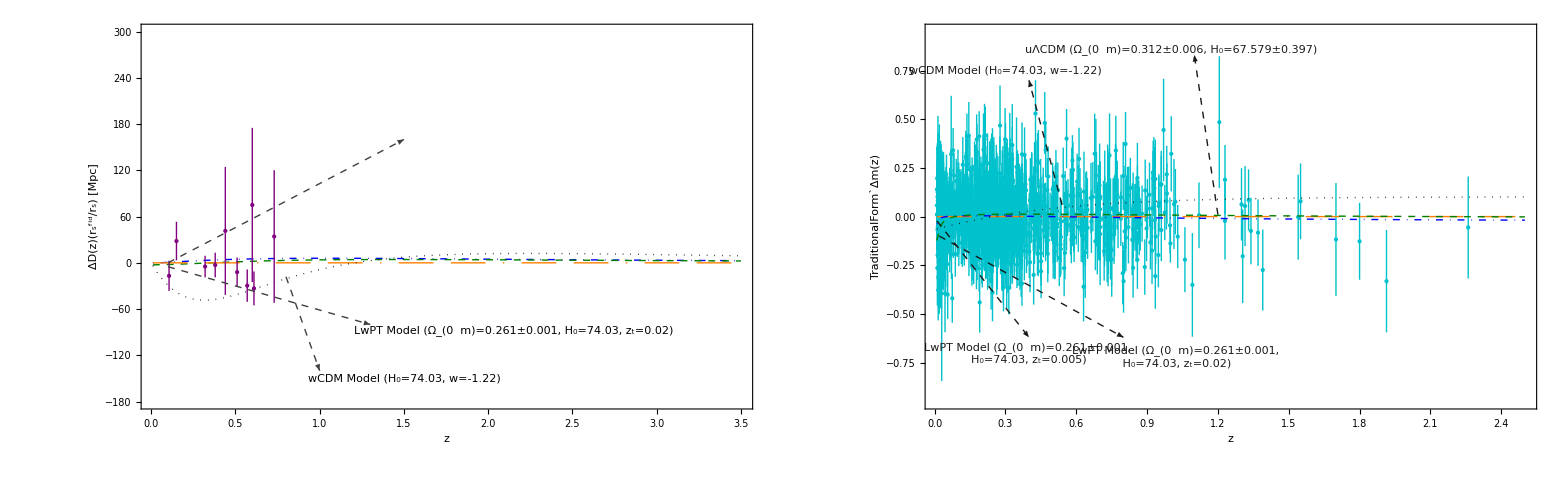

```mathematica
baopanthplot=GraphicsGrid[{{dvplot,dmbplot}},Spacings->0,ImageSize->1900]
```

```mathematica
Export[NotebookDirectory[]<>"baopanthplot.pdf",baopanthplot,ImageResolution->1000];
```

## Table I Calculations

```mathematica
(* Select the corresponding Subscript[z, t] values for the Do loop *)
ztlistab={0.005,0.01,0.02,0.04,0.06,0.08,0.1,0.2};
Length[ztlistab]
```

8

```mathematica
(* This cell takes some time depending on your system so you can skip this cell.*)
(* Do loop to obtain the best fit values of (M, Subscript[Ω, 0m], Subscript[w, 0], Subscript[w, a]) for h=Subscript[h, 0,riess] through NMinimize. This cell takes some time to be completed. Therefore, you can use the following table to run the program without going through the (time-consuming) data acquisition process *)
(*mintotab={};ztw0walistab={};
Do[minhsdtab=NMinimize[{chi2total[M,om,w0,wa,h0riess,1/(1+ztlistab[[p]])],-19.6<M<-19,0.25<om<0.35},{M,om,w0,wa}];
dchitab=minhsdtab[[1]]-minlcdm[[2,1]];
MM=minhsdtab[[2,1,2]];
om0=minhsdtab[[2,2,2]];
w00=minhsdtab[[2,3,2]];
waa=minhsdtab[[2,4,2]];
omh2=minhsdtab[[2,2,2]]*h0riess^2;
AppendTo[mintotab,minhsdtab];
AppendTo[ztw0walistab,{ztlistab[[p]],w00,waa,w00+waa,om0,omh2,MM,dchitab}];
If[Mod[p,2]==0,Print["Finished step ",p," of ",Length[ztlistab], " realizations // Δχ^2=",dchitab," Ω_(0 m)=",om0,", w_0+w_a=",w00+waa," Ω_(0 m)h^2=",omh2," and M=",MM," for z_t=",ztlistab[[p]]]],{p,1,Length[ztlistab]}]*)
```

```mathematica
(* Use this cell instead in order to avoid the (time-consuming) best fit acquisition process *)
ztw0walistab={{0.005,-18.442567843142214,17.437291137251044,-1.0052767058911698,0.26097743240477395,0.14302713945281087,-19.419655001950062,-1.9560589529664867},{0.01,-9.92528972399658,8.924488240030474,-1.0008014839661055,0.2608429518127151,0.14295343815911332,-19.417279149814945,0.8116554197704318},{0.02,-5.275206744040993,4.263663025664592,-1.0115437183764007,0.26072777948942966,0.14289031864800517,-19.402241567916423,9.697755107531293},{0.04,-2.9289914975424582,1.8915647081598612,-1.037426789382597,0.26065671076886376,0.14285136985571517,-19.376634328960446,23.065233851936},{0.06,-2.1880186682401392,1.1282506179470404,-1.0597680502930988,0.260705746894208,0.14287824381440659,-19.35933849018335,31.332198058873928},{0.08,-1.8139797851541253,0.7286634514244823,-1.085316333729643,0.26085201858176577,0.14295840714830693,-19.344493499328724,37.957229497236995},{0.1,-1.5815861253943613,0.46576308430361923,-1.1158230410907422,0.2610840130807408,0.1430855503623827,-19.33065547245205,43.27627624584238},{0.2,-1.220508321898322,-0.01644141872049343,-1.2369497406188155,0.26223729774057636,0.14371760120429325,-19.295302044323297,50.10410164470386}};
```